# NG22P04. Метод k-средних и RBF-сети

КМ2021, курс 2, семестр 4
04-март-2022

### 1. Обучающий и тестирующий наборы

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Dimensions[Data=Import["NG22P04Problem.xlsx",{"Sheets","ГудДВ"}]]
```

{3000,3}

```mathematica
(*Сначала перемешиваем данные с помощью RandomSample и делим*)
```

```mathematica
kmSplit[data_,k_]:=Partition[RandomSample[data],UpTo[Round[k Length[data]]]]
```

```mathematica
{Train,Test}=kmSplit[Data,0.8];
```

```mathematica
Dimensions/@{Train,Test}
```

{{2400,3},{600,3}}

```mathematica
(*Разделим координаты от меток и масшатбируем координаты*)
```

```mathematica
TrainCoord=Train⟦;;,1;;2⟧/20;
TrainLabel=Round[Train⟦;;,3⟧];
```

```mathematica
TestCoord=Test⟦;;,1;;2⟧/20;
TestLabel=Round[Test⟦;;,3⟧];
```

```mathematica
(*Индексы своих и чужих*)
```

```mathematica
friendInd=Flatten[Position[TrainLabel,1]];
foeInd=Flatten[Position[TrainLabel,-1]];
```

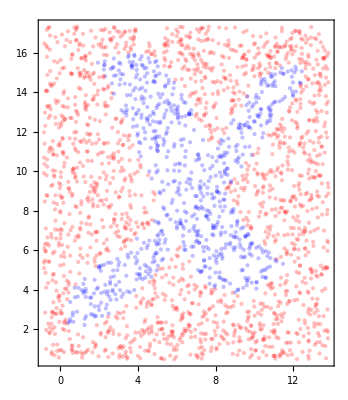

```mathematica
fig=Graphics[
MapThread[{#2/.{1->Blue,-1->Red},Opacity[0.25],Point[#1]}&,{TrainCoord,TrainLabel}],
Frame->True
]
```

### 2. Метод к-средних

```mathematica
(*Центы кластеров*)
```

```mathematica
friendCenter=RandomSample[TrainCoord⟦friendInd⟧,20];
foeCenter=RandomSample[TrainCoord⟦foeInd⟧,40];
```

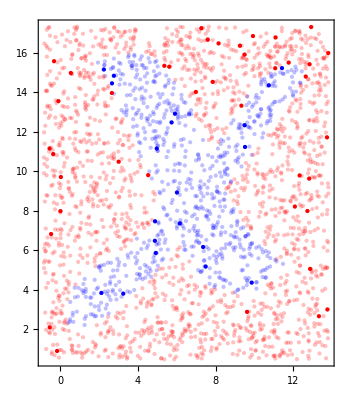

```mathematica
Show[
fig,
Graphics[{Blue,PointSize[Medium],Point[#]}&/@friendCenter],
Graphics[{Red,PointSize[Medium],Point[#]}&/@foeCenter]
]
```

```mathematica
(*С помощью Nearest находим индексы кластеров, к которым принадлежит каждая точка*)
```

```mathematica
friendClusterInd=Flatten[Nearest[friendCenter->"Index",TrainCoord⟦friendInd⟧,1]];
foeClusterInd=Flatten[Nearest[foeCenter->"Index",TrainCoord⟦foeInd⟧,1]];
```

```mathematica
(*Т.к. мы нашли индексы кластеров для каждой точки, то положение данного кластера в списке индексов и будет индексом соответствующей точки*)
```

```mathematica
friendClusters=Flatten[Position[friendClusterInd,#]]&/@Range[20];
foeClusters=Flatten[Position[foeClusterInd,#]]&/@Range[40];
```

```mathematica
(*Находим среднее по всем точкам в каждом кластере, они и будут новыми центрами*)
```

```mathematica
newFriendCenter=Mean[TrainCoord⟦friendInd⟧⟦#⟧]&/@friendClusters;
newFoeCenter=Mean[TrainCoord⟦foeInd⟧⟦#⟧]&/@foeClusters;
```

```mathematica
(*В одном цикле*)
```

```mathematica
newFriendCenter=RandomSample[TrainCoord⟦friendInd⟧,20];
friendCenter={};
While[
friendCenter ≠ newFriendCenter,
friendClusterInd=Flatten[Nearest[newFriendCenter->"Index",TrainCoord⟦friendInd⟧,1]];
friendClusters=Flatten[Position[friendClusterInd,#]]&/@Range[20];
friendCenter=newFriendCenter;
newFriendCenter=Mean[TrainCoord⟦friendInd⟧⟦#⟧]&/@friendClusters;
]
```

```mathematica
newFoeCenter=RandomSample[TrainCoord⟦foeInd⟧,40];
foeCenter={};
While[
foeCenter ≠ newFoeCenter,
foeClusterInd=Flatten[Nearest[newFoeCenter->"Index",TrainCoord⟦foeInd⟧,1]];
foeClusters=Flatten[Position[foeClusterInd,#]]&/@Range[40];
foeCenter=newFoeCenter;
newFoeCenter=Mean[TrainCoord⟦foeInd⟧⟦#⟧]&/@foeClusters;
]
```

```mathematica
(*Финальные центры кластеров*)
```

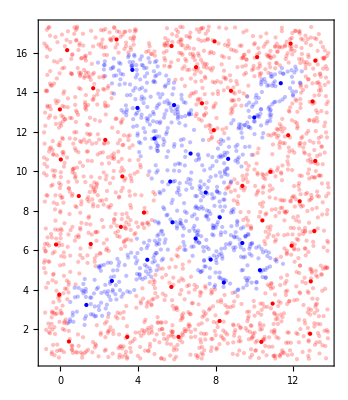

```mathematica
Show[
fig,
Graphics[{Blue,PointSize[Medium],Point[#]}&/@friendCenter],
Graphics[{Red,PointSize[Medium],Point[#]}&/@foeCenter]
]
```

### 3. Зоны влияния

```mathematica
friendCovar=Covariance[TrainCoord⟦friendInd⟧⟦#⟧]&/@friendClusters;
foeCovar=Covariance[TrainCoord⟦foeInd⟧⟦#⟧]&/@foeClusters;
```

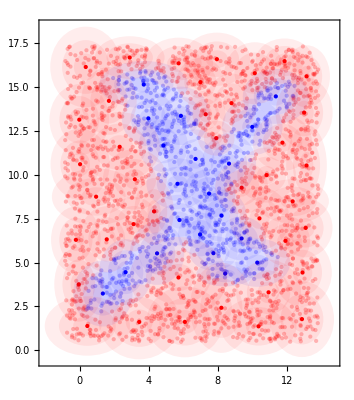

```mathematica
Show[
fig,
Graphics[{Blue,PointSize[Medium],Point[#]}&/@friendCenter],
Graphics[{Red,PointSize[Medium],Point[#]}&/@foeCenter],
Graphics[Table[MapThread[{Blue,Opacity[0.07],Ellipsoid[#1,k^2#2]}&,{friendCenter,friendCovar}],{k,1,3}]],
Graphics[Table[MapThread[{Red,Opacity[0.07],Ellipsoid[#1,k^2#2]}&,{foeCenter,foeCovar}],{k,1,3}]]
]
```

### 4. Радиально-базисные функции

```mathematica
friendCovar⟦1⟧.({x,y}-friendCenter⟦1⟧).({x,y}-friendCenter⟦1⟧)
```

(-10.2907+x) (0.315185 (-10.2907+x)+0.167304 (-4.99771+y))+(0.167304 (-10.2907+x)+0.298736 (-4.99771+y)) (-4.99771+y)

```mathematica
RBF[m_,s_]:=With[
{centers=Join[friendCenter,foeCenter],covars=Join[friendCovar,foeCovar]},
Exp[-1/2 Inverse[(s^2 covars⟦m⟧)].(#-centers⟦m⟧).(#-centers⟦m⟧)]
]&
```

```mathematica
RBF[3,3][{x,y}]
```

ⅇ^(1/2 (-(-6.71334+x) (0.424857 (-6.71334+x)+0.0906807 (-10.9022+y))-(0.0906807 (-6.71334+x)+0.355757 (-10.9022+y)) (-10.9022+y)))

```mathematica
Manipulate[
Plot3D[RBF[m,3][{x,y}],{x,-3,15},{y,-1,17},ColorFunction->"GreenPinkTones",PlotRange->All],
{{m,15,"m"},Range[60]}
]
```

### 5. Псевдообратная матрица

```mathematica
(*Матрица коэффициентов*)
```

```mathematica
Dimensions[M=Table[RBF[m,3][p]//Chop,{p,TrainCoord},{m,1,60}]]
```

{2400,60}

```mathematica
(*Разложение матрицы*)
```

```mathematica
{U,S,V}=SingularValueDecomposition[M];
```

```mathematica
(*Находим неопределенные коэффициенты согласно формулам*)
```

```mathematica
s=Diagonal[S];
```

```mathematica
(η=Uᵀ.TrainLabel)//Dimensions
```

{2400}

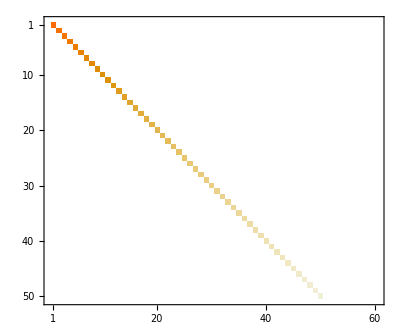

```mathematica
MatrixPlot[S[[;;50]]]
```

```mathematica
ξ=Take[η,60]/s;
```

```mathematica
α=V.ξ;
```

```mathematica
(*Сам классификатор, по умолчанию берем зону влияния s=3*)
```

```mathematica
Classifier[x_,s_:3]:=α.(RBF[#,s][x]&/@Range[60]//Chop)
```

```mathematica
Classifier[{1,2}]
```

-0.165193

### 6. Сеть радиально-базисных функций

```mathematica
Plot3D[Classifier[{x,y}],{x,-3,15},{y,-1,17},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Plot3D[Sign[Classifier[{x,y}]],{x,-1,14},{y,0,17},ColorFunction->"TemperatureMap"]
```

-Graphics3D-

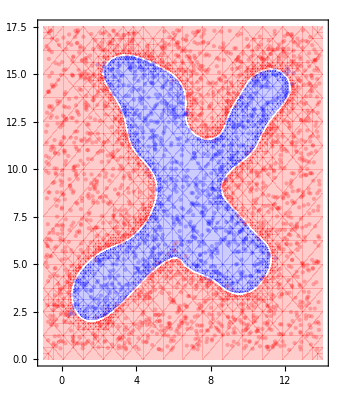

```mathematica
Show[
fig,
ContourPlot[Sign[Classifier[{x,y}]],{x,-1,14},{y,0,17.5},ContourShading->{{Red,Opacity[0.2]},{Blue, Opacity[0.2]}},Contours->{0}]
]
```

```mathematica
(*Судя по графикам, классификатор имеет довольно большую точность*)
```

### 7. Ошибки первого и второго рода

```mathematica
friendIndTest=Flatten[Position[TestLabel,1]];
foeIndTest=Flatten[Position[TestLabel,-1]];
```

```mathematica
(*1-го рода*)
```

```mathematica
pred=Sign[Classifier[#]]&/@TestCoord⟦friendIndTest⟧;
```

```mathematica
Count[pred,-1]/Length[pred]//N//PercentForm
```

PercentForm[0.068323]

```mathematica
(*2-го рода*)
```

```mathematica
pred=Sign[Classifier[#]]&/@TestCoord⟦foeIndTest⟧;
```

```mathematica
Count[pred,1]/Length[pred]//N//PercentForm
```

PercentForm[0.0318907]

```mathematica
(*И на самом деле, классификатор имеет большую точность*)
```

### 8. Зависимость качества классификатора от размеры зоны влияния RBF

```mathematica
(*Графики*)
```

```mathematica
Map[{#,Plot3D[Classifier[{x,y},#],{x,-3,15},{y,-1,17},ColorFunction->"TemperatureMap",PlotPoints->5],
Show[fig,ContourPlot[Sign[Classifier[{x,y},#]],{x,-1,14},{y,0,17.5},ContourShading->{{Red,Opacity[0.2]},{Blue, Opacity[0.2]}},Contours->{0},PlotPoints->7]]
}&,Range[6]
]//Quiet
```

$Aborted

```mathematica
(*Ошибки*)
```

```mathematica
Table[
predfriend=Sign[Classifier[#,s]]&/@TestCoord⟦friendIndTest⟧;
predfoe=Sign[Classifier[#,s]]&/@TestCoord⟦foeIndTest⟧;
{s,(100Count[predfriend,-1])/Length[predfriend]//N,(100Count[predfoe,1])/Length[predfoe]//N},
{s,1,6}]//Quiet
```

{{1,23.7838,19.759},{2,13.5135,11.8072},{3,2.7027,4.09639},{4,21.6216,10.3614},{5,30.8108,14.4578},{6,36.2162,15.9036}}

```mathematica
(*Как можно заметить, наилучшее качество распознавания достигается при s=3, при остальных значениях оно ухудшается. Причем ошибка второго рода наибольшая при s<3, а ошибка первого рода при s>3*)
```